Global package :

```mathematica
TripleFromFigure[fig_,K_]:={(#-Mod[#,2]-2Mod[(#-Mod[#,2])/2,K])/(2K),Mod[(#-Mod[#,2])/2,K],Mod[#,2]}&[fig];FigureFromTriple[{σ_,κ_,δ_},K_]:=σ 2 K+2 κ +δ;MyInstructionsTable[nb_,{S_,K_}]:=Thread[Flatten[Table[{i,j},{i,S-1,0,-1},{j,K-1,0,-1}],1]->({(#-Mod[#,2]-2Mod[(#-Mod[#,2])/2,K])/(2K),Mod[(#-Mod[#,2])/2,K],Mod[#,2]}&/@PadLeft[IntegerDigits[nb,2S K],S K])];Base4SActiveTriples[nb_,{S_,K_}]:=PadLeft[IntegerDigits[nb,2S K],S K]          (*UTILE ? codeofactivetriples, activefigure*);MTNumberFromTriples[mytriplets_,{S_,K_}]:=FromDigits[Thread[FigureFromTriplet[#,2]&[mytriplets]],2S K];ChangeNumbering[number_,{S_,K_}]:=FromDigits[Flatten[Reverse[Partition[PadLeft[IntegerDigits[number,2S K],S K],2]]],2S K];
SBTM[s_,nb_,limit_]:=Module[{k=2,tm},{tm=TuringMachine[{ChangeNumbering[nb,{s,2}],s,k},{{1,0},{{},0}},limit];
step=If[MemberQ[Transpose[Transpose[tm][[1]]][[3]],1],First[Position[Transpose[Transpose[tm][[1]]][[3]],1]][[1]],limit]-1;Clear[tm];tm=TuringMachine[{ChangeNumbering[nb,{s,2}],s,k},{{1,0},{{},0}},step];
delta=If[1-Min[Transpose[Transpose[tm][[1]]][[3]]]>0,1-Min[Transpose[Transpose[tm][[1]]][[3]]],0];
tm12=Transpose[Transpose[tm][[1]]][[2]];tm11=Transpose[Transpose[tm][[1]]][[1]];f[nb]=ArrayPlot[Last/@tm,Mesh->True,PlotLabel->{s,k,nb},LabelStyle->Directive[Bold],Epilog->{{Red,Thick,Line[{{delta,0},{delta,step+1}}]},Orange,Thickness[0.15/(step+1)],Arrowheads[0.5/(step+1)],Table[Rotate[Arrow[{{-1/2+tm12[[i]],2/10+1+step-i},{-1/2+tm12[[i]],4/5+1+step-i}}],-2π/s(tm11[[i]]-1)],{i,step+1}]}]};f[nb]];
activetriples[nb_,{s_,k_}]:=MyInstructionsTable[nb,{s,k}][[All,2]];
Base4SEvolution[s_,nb_,limit_]:=Module[{k=2,a,sigma=0,activatedtriple},i=0;a[_]=0;n=ninf=-1;sigma=0;figures={};res={{1,0,-1,{0}}};While[n<0 && i<limit,{activatedtriple=activetriples[nb,{s,k}][[2s-2sigma-a[n]]];a[n]=activatedtriple[[2]];n=n-1+2activatedtriple[[3]];ninf=Min[n,ninf];sigma=activatedtriple[[1]]};figures=AppendTo[figures,FigureFromTriple[activatedtriple,2]];res=AppendTo[res,{i+2,sigma,n,Table[a[j],{j,ninf,n}]}];i++];figures];
SingleTMStep[rule_, {s_, tape_, pos_} /; pos>Length[tape]] := SingleTMStep[rule,{s, Prepend[tape,0], pos}]
SingleTMStep[rule_, {s_, tape_, pos_}] := Apply[{#1,ReplacePart[tape,#2,-pos],pos-#3}&,Replace[{s,tape[[-pos]]},rule]]
SingleTMEvolve[rule_, tape_, bound_] := NestWhile[SingleTMStep[rule, #]&, {1,tape,1}, ( 18>#[[3]]>0)&,1,bound]  (*  !!!!!!!!!  *)
SingleTMEvolveList[rule_, tape_, bound_] := NestWhileList[SingleTMStep[rule, #]&, {1,tape,1},( 18>#[[3]]>0)&,1,bound]   (*  !!!!!!!!!  *)
WolframInstructionsTable[nb_,{S_,K_}]:=Thread[Flatten[Table[{i+1,j},{i,S-1,0,-1},{j,K-1,0,-1}],1]->({(#-Mod[#,2]-2Mod[(#-Mod[#,2])/2,K])/(2K)+1,Mod[(#-Mod[#,2])/2,K],2Mod[#,2]-1}&/@PadLeft[IntegerDigits[nb,2S K],S K])]
conjugate[li_]:=li/.{0->u,1->v}/.{u->1,v->0};classsym[nb_,S_]:=Table[FromDigits[Partition[Flatten[Map[Append[#,Last[Partition[PadLeft[IntegerDigits[nb,4S],2S],2]]]&,Permutations[Take[Partition[PadLeft[IntegerDigits[nb,4S],2S],2],S-1]]]],2S][[n]]/.Table[Flatten[Table[ 4j+m->4(S-Transpose[Position[Permutations[Reverse[Range[S-1]]],j]][[2]])[[k]]+m,{j,S-1},{m,0,3}]],{k,(S-1)!}][[n]],4S],{n,Length[Permutations[Take[Partition[PadLeft[IntegerDigits[nb,4S],2S],2],S-1]]]}];
```

```mathematica
Grid[MapThread[Prepend,{Prepend[Table[(2s k)^(s k),{s,2,5},{k,2,5}],{"s"->2,"s"->3,"s"->4,"s"->5}],{"","k"->2,"k"->3,"k"->4,"k"->5}}],Frame->All,Background->{None,{None,Yellow}}]
```

| s→2 | s→3 | s→4 | s→5
k→2 | 4096 | 2985984 | 4294967296 | 10240000000000
k→3 | 2985984 | 198359290368 | 36520347436056576 | 14348907000000000000000
k→4 | 4294967296 | 36520347436056576 | 1208925819614629174706176 | 109951162777600000000000000000000
k→5 | 10240000000000 | 14348907000000000000000 | 109951162777600000000000000000000 | 2980232238769531250000000000000000000000000

```mathematica
ChangeNumbering[number_,{S_,K_}]:=FromDigits[Flatten[Reverse[Partition[PadLeft[IntegerDigits[number,2S K],S K],2]]],2S K]
```

```mathematica
activetriplets[nb_]:=({(#-Mod[#,2]-2Mod[(#-Mod[#,2])/2,2])/4,Mod[(#-Mod[#,2])/2,2],Mod[#,2]}&/@PadLeft[IntegerDigits[nb,16],8])
```

```mathematica
activetriplets[1]
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,1}}

```mathematica
rules1=Thread[Partition[Flatten[Permutations[Partition[Range[15,4,-1],4]]],12]->Table[Range[15,4,-1],{6}]]
```

{{15,14,13,12,11,10,9,8,7,6,5,4}→{15,14,13,12,11,10,9,8,7,6,5,4},{15,14,13,12,7,6,5,4,11,10,9,8}→{15,14,13,12,11,10,9,8,7,6,5,4},{11,10,9,8,15,14,13,12,7,6,5,4}→{15,14,13,12,11,10,9,8,7,6,5,4},{11,10,9,8,7,6,5,4,15,14,13,12}→{15,14,13,12,11,10,9,8,7,6,5,4},{7,6,5,4,15,14,13,12,11,10,9,8}→{15,14,13,12,11,10,9,8,7,6,5,4},{7,6,5,4,11,10,9,8,15,14,13,12}→{15,14,13,12,11,10,9,8,7,6,5,4}}

```mathematica
rules=Table[Thread[rules1[[k]]],{k,6}]
```

{{15→15,14→14,13→13,12→12,11→11,10→10,9→9,8→8,7→7,6→6,5→5,4→4},{15→15,14→14,13→13,12→12,7→11,6→10,5→9,4→8,11→7,10→6,9→5,8→4},{11→15,10→14,9→13,8→12,15→11,14→10,13→9,12→8,7→7,6→6,5→5,4→4},{11→15,10→14,9→13,8→12,7→11,6→10,5→9,4→8,15→7,14→6,13→5,12→4},{7→15,6→14,5→13,4→12,15→11,14→10,13→9,12→8,11→7,10→6,9→5,8→4},{7→15,6→14,5→13,4→12,11→11,10→10,9→9,8→8,15→7,14→6,13→5,12→4}}

```mathematica
Permutations[{1,2,3}]
```

{{1,2,3},{1,3,2},{2,1,3},{2,3,1},{3,1,2},{3,2,1}}

```mathematica
sym4[nb_]:=Module[{},{u=Partition[PadLeft[IntegerDigits[nb,16],8],2]};     FromDigits[#,16]&/@MapThread[ReplaceAll,{Partition[Flatten[    Map[Append[#,Last[u]]&,   (Permute[    Most[u],#]& /@{{1,2,3},{1,3,2},{2,1,3},{2,3,1},{3,1,2},{3,2,1}})      ]],8],rules  }]]         (*OK !*)
```

```mathematica
sym4[1000000]
```

{1000000,8523648,184566336,125960320,3254782912,3255238848}

```mathematica
sym4[3254782912]
```

{3254782912,3255238848,8523648,1000000,125960320,184566336}

```mathematica
u=BinCounts[Table[Length[DeleteDuplicates[sym4[RandomInteger[4294967296]]]],{i,20000000}],{1,7,1}]
```

{6,12,14886,0,0,19985096}

```mathematica
Total[%]
```

20000000

```mathematica
(*Inventaire complet : Multi Run : on est proche de l'optimum quand S=3 lorsqu'on complète i<3 par i<6, 12, 29*)   t=AbsoluteTime[];
```

```mathematica
(*First Run : i<3, on élimine les symétriques*)       t=AbsoluteTime[];loop=halt=0;remise={};nb=0;
remise=Reap[     While[ nb<4294967(*296*),w=DeleteDuplicates[sym4[nb]];lw=Length[w];
If[ nb>Min[w],     ,{ Clear[a]; i=0;a[_]=0;n=ninf=-1;sigma=0;res={{0,-1,{0}}};

While[n<0 && i<3,{activatedtriplet=activetriplets[nb][[8-2sigma-a[n]]];a[n]=activatedtriplet[[2]];n=n-1+2activatedtriplet[[3]];ninf=Min[n,ninf];sigma=activatedtriplet[[1]];res=AppendTo[res,{sigma,n,Table[a[j],{j,ninf,n}]}]   };i++];

If[n==0,halt=halt+lw,    {corners=#[[1]]&/@Position[res,-1,2];left=Min[#[[2]]&/@res];Do[{corners=AppendTo[corners,Select[#[[1]]&/@Position[res,k,2],#>Max[corners]&]]},{k,-2,left,-1}];listetest={#[[1]],FromDigits[#[[3]],2]}&/@res[[Flatten[corners]]];If[Length[Union[listetest]]≠Length[listetest],loop=loop+lw,Sow[#]&/@w]}    ]     }    ]     ;nb=nb+2]     ][[2,1]];
   AbsoluteTime[]-t
```

775.0415614

```mathematica
{halt,loop,Length[remise]}
```

{1039758,8635538,1438728}

```mathematica
(*Following Runs : i<6, 12, 24, ..., 192*) t=AbsoluteTime[];Do[j=1;
remise=Reap[     While[j<Length[remise],nb=remise[[j]];w=DeleteDuplicates[sym4[nb]];lw=Length[w];
If[nb>Min[w],   ,{Clear[a]; i=0;a[_]=0;n=ninf=-1;sigma=0;res={{0,-1,{0}}};

While[n<0 && i<jj,{activatedtriplet=activetriplets[nb][[8-2sigma-a[n]]];a[n]=activatedtriplet[[2]];n=n-1+2activatedtriplet[[3]];ninf=Min[n,ninf];sigma=activatedtriplet[[1]];res=AppendTo[res,{sigma,n,Table[a[j],{j,ninf,n}]}]   };i++];

If[n==0,halt=halt+lw,    {corners=#[[1]]&/@Position[res,-1,2];left=Min[#[[2]]&/@res];Do[{corners=AppendTo[corners,Select[#[[1]]&/@Position[res,k,2],#>Max[corners]&]]},{k,-2,left,-1}];listetest={#[[1]],FromDigits[#[[3]],2]}&/@res[[Flatten[corners]]];If[Length[Union[listetest]]≠Length[listetest],loop=loop+lw,Sow[#]&/@w]}    ]     }     ];j++]    ][[2,1]],{jj,{6,12,24,48,96,192}}];      
    
AbsoluteTime[]-t
```

359.9862323

```mathematica
{halt,loop,Length[remise]}
```

{1301739,9810935,1350}

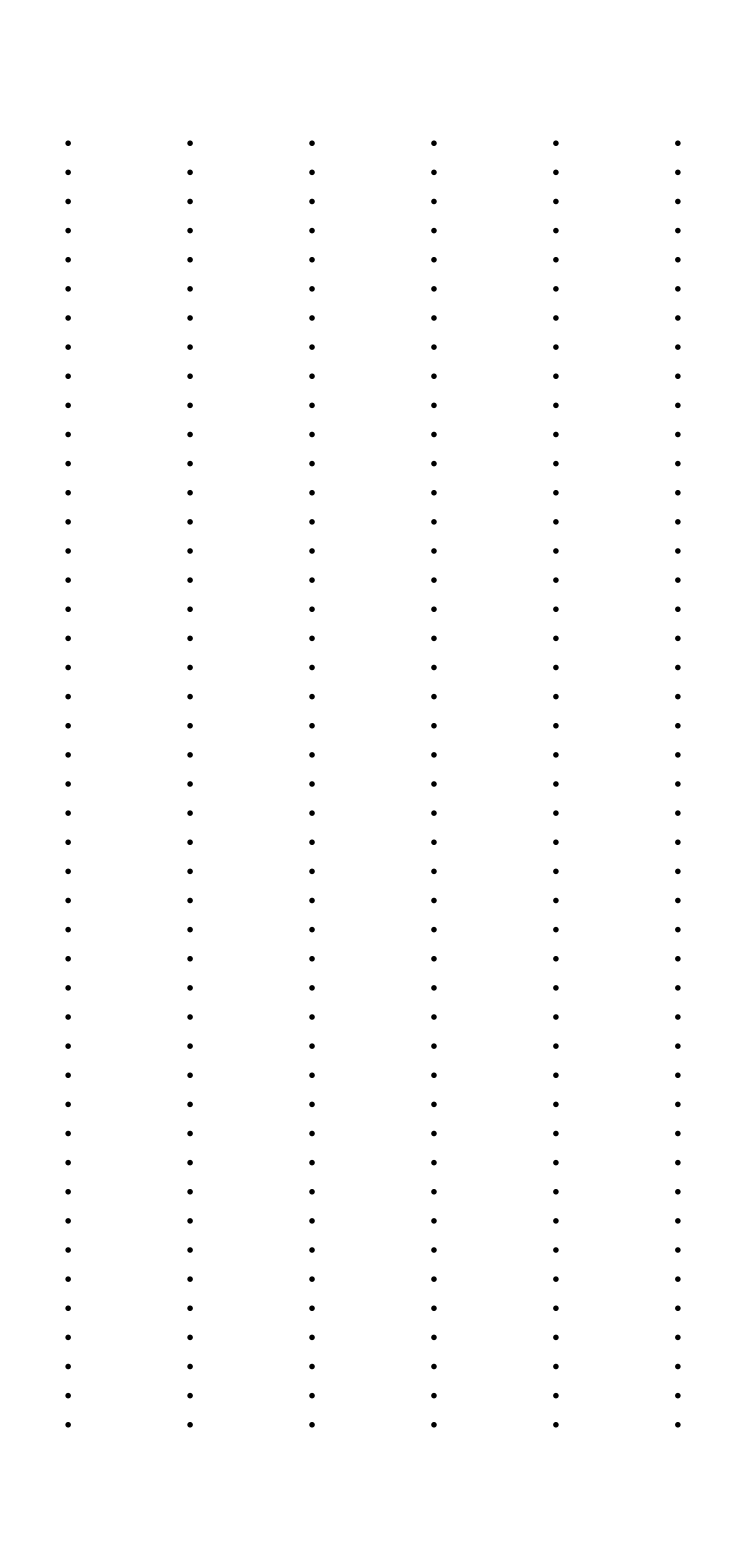

```mathematica
GraphicsGrid[Partition[Table[SBTM[4,remise[[j]],50],{j,1,Length[remise],5}],6]]
```

```mathematica
sym4[
```